# Relation between px and Ax

## Init

```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True]
ClearAll["Global`*"]
Needs["NumericalCalculus`"]
$Assumptions={_∈Reals,-Pi<θ<Pi &&-Pi<ϕ<Pi && -Pi<φ<Pi && -Pi<δ<Pi && c > 0 && ω >0 && w0>0 && z >0 && h >0 && E0 > 0 && r >0 && l∈Reals && x∈Reals && y ∈Reals &&t>0 && β∈Reals && α∈Reals && γ∈Reals}
rule2carte ={r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
rule2pol = {x->r Cos[θ],y-> r Sin[θ]};
k := ω/c
zR:=1/2*k*w0^2 (*Rayleigh range*)
w[z] := w0 *Sqrt[1+(z/zR)^2] (* Beam radius *)
R[z] := z*(1+(zR/z)^2) (* Radius of curvature *)
p:=0
n := Abs[l]+2*p
G[z]:= (n+1)ArcTan[z/zR](* Gouy phase at z *)
Gpl := Sqrt[(2*Factorial[p])/(Pi*Factorial[p+Abs[l]])]*0+1
Lp := 1(* generalized Laguerre polynomials p = 0 -> Lp = 1 *)
If[p ==1,Lp = 1 +Abs[l]-(2*r^2)/w[z]^2]
f[r]=(w0*Gpl)/w[z]((r √2)/w[z])^Abs[l]*Exp[-r^2/w[z]^2]
u[r,θ,z]:=Evaluate[f[r]*Lp*Exp[-I k r^2/(2 R[z])]*Exp[-I*l*θ]*Exp[I*G[z]]](*((2r^2)/w[z]^2)*)
tempEnv = Exp[-(t-z)^2/Tp^2]

Ex[r,θ,z]=E0*u[r,θ,z]*Exp[-I*k*z+I*ω*t]; (**tempEnv*)
Ey[r,θ,z]=0;
Ez[r,θ,z]=0;

Ex[x,y,z] =Ex[r,θ,z]/. {r->Norm[{x,y}],θ->ArcTan[x,y]};

Clear[l]
l=1;
c = 1;
ω = 1;
φ=0;
Ev = Evaluate[{Ex[x,y,z],0,0}]/.{Abs[x]->RealAbs[x],Abs[y]->RealAbs[y]}//Simplify
```

{_∈ℝ,-π<θ<π&&-π<ϕ<π&&-π<φ<π&&-π<δ<π&&c>0&&ω>0&&w0>0&&z>0&&h>0&&E0>0&&r>0&&l∈ℝ&&x∈ℝ&&y∈ℝ&&t>0&&β∈ℝ&&α∈ℝ&&γ∈ℝ}

(2^(Abs[l]/2) ⅇ^(-r^2/(w0^2 (1+(4 c^2 z^2)/(w0^4 ω^2)))) (r/(w0 √(1+(4 c^2 z^2)/(w0^4 ω^2))))^Abs[l])/(√(1+(4 c^2 z^2)/(w0^4 ω^2)))

ⅇ^(-(t-z)^2/Tp^2)

{(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 √(x^2+y^2))/(w0^4+4 z^2),0,0}

```mathematica
EzCP=-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](-2*I*E0* α *ω*Exp[-(ⅈ (α^2+β^2-ⅈ φ-γ φ-ⅈ t ω-t γ ω-ⅈ ArcTan[γ]-γ ArcTan[γ]))/(ⅈ+γ)])/(c h (ⅈ+γ) √(1+γ^2))/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}
EzO3=Evaluate[-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](√2 ⅇ^(-1/2 ⅈ ((2 α^2)/(ⅈ+γ)+(2 β^2)/(ⅈ+γ)-2 (φ+t ω)-4 ArcTan[γ])) E0 (ⅈ-2 ⅈ α^2-2 α β+γ) ω)/(c h (-ⅈ+γ) (ⅈ+γ)^2)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}]; (*L=1*)
EzO5=-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](-2 ⅈ √2 ⅇ^(-(ⅈ (2 α^2+2 β^2+(ⅈ+γ) (-2 (φ+t ω))))/(2 (ⅈ+γ))) E0 (-2 α^4+2 ⅈ α^3 β+2 ⅈ α β (-3+β^2+3 ⅈ γ)+α^2 (7-2 β^2-7 ⅈ γ)+(ⅈ+γ) (2 ⅈ-ⅈ β^2+2 γ)) ω)/(c h^3 (ⅈ+γ)^5)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}(*L=l*);
EzLGO3 = EzO3 ;
EzLGO5 = EzO3 +EzO5;
```

-(2 ⅇ^(-ⅈ z-(ⅈ (-ⅈ t+x^2/w0^2+y^2/w0^2-(2 t z)/w0^2-ⅈ ArcTan[(2 z)/w0^2]-(2 z ArcTan[(2 z)/w0^2])/w0^2))/(ⅈ+(2 z)/w0^2)) E0 x)/(w0^2 (ⅈ+(2 z)/w0^2) √(1+(4 z^2)/w0^4))

```mathematica
(* Ax dAy/dy - Ay * dAy/dy -->  Az dAx/dx - Ax * dAz/dx  *)
Ex= Ev[[1]]
Ez = EzO3
```

(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 √(x^2+y^2))/(w0^4+4 z^2)

-(ⅈ √2 ⅇ^(-ⅈ z-1/2 ⅈ (-2 t+(2 x^2)/(w0^2 (ⅈ+(2 z)/w0^2))+(2 y^2)/(w0^2 (ⅈ+(2 z)/w0^2))-4 ArcTan[(2 z)/w0^2])) E0 (ⅈ-(2 ⅈ x^2)/w0^2-(2 x y)/w0^2+(2 z)/w0^2))/(w0 (-ⅈ+(2 z)/w0^2) (ⅈ+(2 z)/w0^2)^2)

```mathematica
termA = Ez*D[Ez,z]//Simplify
termAb = Ez*D[Ex,x]//Simplify
termB = Ex*D[Ez,x]//Simplify

eps = Simplify[termA+termB]
epsb = Simplify[termAb+termB]
```

(2 ⅇ^((t (2 ⅈ w0^2+4 z)-2 (x^2+y^2+ⅈ w0^2 z+2 z^2)+(4 ⅈ w0^2+8 z) ArcTan[(2 z)/w0^2])/(w0^2-2 ⅈ z)) E0^2 w0^6 (ⅈ w0^2-2 ⅈ x^2-2 x y+2 z) (w0^6-2 w0^4 (2+x^2-ⅈ x y+3 ⅈ z)+2 w0^2 (y^2+x^2 (7+4 ⅈ z)+8 ⅈ z-6 z^2+2 x y (-3 ⅈ+2 z))-4 (x^4-ⅈ x^3 y+x^2 (y^2+(7 ⅈ-2 z) z)+x y (-ⅈ y^2+2 (3+ⅈ z) z)+ⅈ z (y^2-2 z (-2 ⅈ+z)))))/((w0^2-2 ⅈ z)^6 (w0^2+2 ⅈ z)^2)

(2 ⅇ^((2 ⅈ t w0^2-2 x^2-2 y^2+4 t z-2 ⅈ w0^2 z-4 z^2+(4 ⅈ w0^2+8 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0^2 w0^6 (-ⅈ x+y) (w0^2-2 x^2+2 ⅈ x y-2 ⅈ z)^2)/(√(x^2+y^2) (w0^2-2 ⅈ z)^4 (w0^2+2 ⅈ z)^2)

(4 ⅇ^((2 ⅈ t w0^2-2 x^2-2 y^2+4 t z-2 ⅈ w0^2 z-4 z^2+(4 ⅈ w0^2+8 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0^2 w0^6 √(x^2+y^2) (w0^2 (3 ⅈ x+y)-2 ⅈ (x^3-ⅈ x^2 y+3 ⅈ x z+y z)))/((w0^2-2 ⅈ z)^4 (w0^2+2 ⅈ z)^2)

1/((w0^2-2 ⅈ z)^6 (w0^2+2 ⅈ z)^2)2 E0^2 w0^6 (2 ⅇ^((2 ⅈ t w0^2-2 x^2-2 y^2+4 t z-2 ⅈ w0^2 z-4 z^2+(4 ⅈ w0^2+8 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) √(x^2+y^2) (w0^2-2 ⅈ z)^2 (w0^2 (3 ⅈ x+y)-2 ⅈ (x^3-ⅈ x^2 y+3 ⅈ x z+y z))+ⅇ^((t (2 ⅈ w0^2+4 z)-2 (x^2+y^2+ⅈ w0^2 z+2 z^2)+(4 ⅈ w0^2+8 z) ArcTan[(2 z)/w0^2])/(w0^2-2 ⅈ z)) (ⅈ w0^2-2 ⅈ x^2-2 x y+2 z) (w0^6-2 w0^4 (2+x^2-ⅈ x y+3 ⅈ z)+2 w0^2 (y^2+x^2 (7+4 ⅈ z)+8 ⅈ z-6 z^2+2 x y (-3 ⅈ+2 z))-4 (x^4-ⅈ x^3 y+x^2 (y^2+(7 ⅈ-2 z) z)+x y (-ⅈ y^2+2 (3+ⅈ z) z)+ⅈ z (y^2-2 z (-2 ⅈ+z)))))

(2 ⅇ^((2 ⅈ t w0^2-2 x^2-2 y^2+4 t z-2 ⅈ w0^2 z-4 z^2+(4 ⅈ w0^2+8 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0^2 w0^6 (-ⅈ x+y) (w0^4-2 w0^2 (5 x^2-6 ⅈ x y-y^2+2 ⅈ z)+4 (2 x^4-4 ⅈ x^3 y+x^2 (-2 y^2+5 ⅈ z)+6 x y z+(-ⅈ y^2-z) z)))/(√(x^2+y^2) (w0^2-2 ⅈ z)^4 (w0^2+2 ⅈ z)^2)

```mathematica
D[p0[t,x]*Cos[t-x],x]
D[p0[t,x]*Cos[t-x],t]
```

p0[t,x] Sin[t-x]+Cos[t-x] p0^(0,1)[t,x]

-p0[t,x] Sin[t-x]+Cos[t-x] p0^(1,0)[t,x]

```mathematica
eq = D[p0*Cos[t-x]+A0*Cos[t-x],t]==-p0*Cos[t-x]*D[p0*Cos[t-x],x]
Solve[eq,p0]

(*Solve the system numerically with NDSolve*)
solution=NDSolve[eqns,{vx[t,x],x},{t,0,10},{x,0,10}];

(*Extract the solution for vx[t,x] and x[t]*)
(*vxSolution[t_,x_]=vx[t,x]/. solution[[1]];
xSolution[t_]=x[t]/. solution[[1]];

(*Plot vx[t,x] or x[t] to visualize the solution*)
Plot3D[vxSolution[t,x],{t,0,10},{x,0,10},PlotLabel->"vx[t, x]"]*)
```

-A0 Sin[t-x]-p0 Sin[t-x]==-p0^2 Cos[t-x] Sin[t-x]

{{p0→1/2 (1-√(1+4 A0 Cos[t-x])) Sec[t-x]},{p0→1/2 (1+√(1+4 A0 Cos[t-x])) Sec[t-x]}}

NDSolve::ivhead: The independent variable x appears in the head of the expression x[0]. The independent variables should always be arguments.

```mathematica
(*eq = Dt[vx[t,x[t]],t] == D[Ax[t,x[t]],t]*)
eq = D[vx[t,x]+Ax[t,x],t] == vx[t,x[t]]*D[Ax[t,x],x]
Solve[eq,vx[t,x[t]],{x,t}]
```

Ax^(1,0)[t,x]+vx^(1,0)[t,x]==vx[t,x[t]] Ax^(0,1)[t,x]

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[Ax^(1,0)[t,x]+vx^(1,0)[t,x]==vx[t,x[t]] Ax^(0,1)[t,x],vx[t,x[t]],{x,t}]

## Numerical

-0.000884292-0.00895962 ⅈ

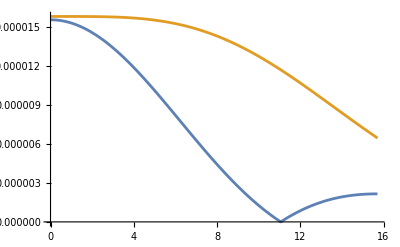

```mathematica
l0=2*Pi;
w0 = 2.5*l0;
E0=0.1;
a0=E0;

x=10^-20;
y =0;
z=0.1;
t=10*l0;
Ez
Plot[{Abs[Re[eps]],Abs[Re[epsb]]},{y,0.001,w0}]
```

```mathematica
Re[termB]//Simplify
```

3.83758×10^-47

```mathematica
ExCP
```

ExCP